### Parameter and function definitions

#### Clear notebook

```mathematica
ClearAll["Global`*"];
```

#### Rate and diffusion constants

```mathematica
fac=10^0;
kAct=fac*2*10^4; (* mM^-1 s^-1 activation rate of calcium *)
kInact = fac*10^2; (* s^-1 inactivation rate of calcium *)
kTrap = fac*3*10^4; (* mM^-1 s^-1 trapping rate of calcium by DMNP *)
kRel = fac*7*10^4; (* s^-1 release rate of calcium by DMNP when light is on*)
kIBind =fac* 10^4; (* mM^-1 s^-1 binding rate of inactivated TCB2 *)
kIUnbind =fac* 1; (* s^-1 unbinding rate of inactivated TCB2 *)
kABind = fac*10^4; (* mM^-1 s^-1 binding rate of activated TCB2 *)
kAUnbind = fac*0; (* s^-1 unbinding rate of activated TCB2 *)

CSat = 6.5; (* mM, saturation concentration of bound TCB2 *)

DT = 5; (* μm^2/s, diffusion constant for TCB2 *)
DD =10; (* μm^2/s, diffusion constant for DMNP *)
DC = 50;(* μm^2/s, diffusion constant for calcium *)
```

#### Initial values

```mathematica
CDI0=0; (* mM *)
CDA0=0; (* mM *)
CBI0=1; (* mM *)
CBA0=0; (* mM *)
CC0=0; (* mM *)
CDst0=20; (* mM *)
CD0=20; (* mM *)
```

#### Domain values

```mathematica
xMax = 200; (* μm *)
yMax = 200; (* μm *)
tMax = 100; (* s *)
```

#### Light activation values

```mathematica
width = 5; (* mm, width of gaussian beam *)
r0 =30; (* mm, radius of circle *)
cyc = 20;
len = 5;
del = 1;
```

### Function definitions

#### Helper functions

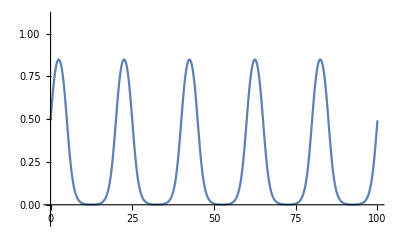

```mathematica
BS[CB_]:=CSat^2/4-(CB-CSat/2)^2; (* concentration of available binding sites *)
gaussian[r_,r0_,s_]:=Exp[-1/2((r-r0)/s)^2];
spaceFunc[r_,r0_,s_]:=1/2*(1-Tanh[(r-r0)/s]);

rFunc[x_,y_,x0_,y0_]:=Sqrt[(x-x0)^2+(y-y0)^2];

Sigmoid[x_]:=1/(1+Exp[-x]);
SmoothBump[x_,a_,xa_,xb_]:=Sigmoid[(x-xa)/a]-Sigmoid[(x-xb)/a]
WaveFunc[t_,cyc_,len_,del_]:=Sum[SmoothBump[t,del,cyc*i,cyc*i+len],{i,0,Floor[tMax/cyc]}];
γFunc[x_,y_,t_]:=spaceFunc[rFunc[x,y,xMax/2,yMax/2],r0,width]*WaveFunc[t,cyc,len,del];(* external light field *)
γFunc[x_,y_,t_]:=spaceFunc[rFunc[x,y,xMax/2,yMax/2],r0,width];(* external light field *)
trange = Range[0,tMax,0.01];
wPoints = WaveFunc[trange,cyc,len,del];
data = Transpose[{trange,wPoints}];
iFun = Interpolation[data];
gamFunc[x_,y_,t_]:=spaceFunc[rFunc[x,y,xMax/2,yMax/2],r0,width]*WaveFunc[t,cyc,len,del];
gamFunc[x_,y_,t_]:=spaceFunc[rFunc[x,y,xMax/2,yMax/2],r0,width]*iFun[t];
pA[CBA_,CBI_]:=CBA/(CBA+CBI);

g[CBA_,CBI_]:=1-(1-gMin)*pA[CBA,CBI];
Plot[WaveFunc[t,cyc,len,del],{t,0,tMax},PlotRange->{-0.1,1.1}]
```

```mathematica
Manipulate[Plot3D[γFunc[x,y,t],{x,0,xMax},{y,0,yMax},PlotRange->{0,1.1},PlotPoints->50],{t,0,tMax}]
```

Plot3D::plln: Limiting value xMax in {x,0,xMax} is not a machine-sized real number.

#### Chemical rate equations

```mathematica
RDI[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kAct*CDI*CC + kInact*CDA-kIBind*CDI*BS[CBA + CBI] + kIUnbind*CBI;
RDA[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=kAct*CDI*CC - kInact*CDA-kABind*CDA*BS[CBA + CBI]+kAUnbind*CBA;

RBI[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kAct*CBI*CC+kInact*CBA+kIBind*CDI*BS[CBA + CBI]-kIUnbind*CBI;
RBA[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=kAct*CBI*CC-kInact*CBA+kABind*CDA*BS[CBA + CBI]-kAUnbind*CBA;

RC[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kAct*(CDI+CBI)*CC + kInact*(CDA+CBA)-kTrap*CDst*CC+kRel*γFunc[x,y,t]*CD;
RD[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=kTrap*CDst*CC-kRel*γFunc[x,y,t]*CD;
RDst[x_,y_,t_,CDI_,CDA_,CBI_,CBA_,CC_,CD_,CDst_]:=-kTrap*CDst*CC+kRel*γFunc[x,y,t]*CD;
```

#### Mechanical force function

```mathematica
gradpA[ind_,CBA_,CBI_]:=(1-gMin)/(CBA+CBI)*((1-pA[CBA,CBI])*D[CBA,ind] + pA[CBA,CBI]*D[CBI,ind]);
strainxx[ux_,uy_]:=D[ux,x];
strainxy[ux_,uy_]:=1/2(D[ux,y]+D[uy,x]);
strainyx[ux_,uy_]:=strainxy[ux,uy];
strainyy[ux_,uy_]:=D[uy,y];
divu[ux_,uy_]:=D[ux,x]+D[uy,y];
gradiTr[ind_,ux_,uy_]:=D[divu[ux,uy],ind];

lapui[ui_]:=D[ui,{x,2}]+D[ui,{y,2}]
forcex[x_,y_,ux_,uy_,CBA_,CBI_]:= 2 μ0 *(
 ((D[CBA+CBI,x]*strainxx[ux,uy] +D[CBA+CBI,y]*strainxy[ux,uy])
-1/2 g[CBA,CBI]*D[CBA+CBI,x])+(CBA+CBI)*(1/2(gradiTr[x,ux,uy] + lapui[ux]) - 1/2 gradpA[x,CBA,CBI]))+λ0*(D[CBA+CBI,x]*(divu[ux,uy] - g[CBA,CBI])+(CBA+CBI)*(gradiTr[x,ux,uy]-gradpA[x,CBA,CBI]));

forcey[x_,y_,ux_,uy_,CBA_,CBI_]:= 2 μ0 *(
 ((D[CBA+CBI,x]*strainyx[ux,uy] +D[CBA+CBI,y]*strainyy[ux,uy])
-1/2 g[CBA,CBI]*D[CBA+CBI,y])+(CBA+CBI)*(1/2(gradiTr[y,ux,uy] + lapui[uy]) - 1/2 gradpA[y,CBA,CBI]))+λ0*(D[CBA+CBI,y]*(divu[ux,uy] - g[CBA,CBI])+(CBA+CBI)*(gradiTr[y,ux,uy]-gradpA[y,CBA,CBI]));
```

### Set up differential equation

#### Define differential equations

```mathematica
pdes={
D[CDI[x,y,t],t]==RDI[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DT*Laplacian[CDI[x,y,t],{x,y}],
D[CDA[x,y,t],t]==RDA[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DT*Laplacian[CDA[x,y,t],{x,y}],

D[CBI[x,y,t],t]==RBI[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]],
D[CBA[x,y,t],t]==RBA[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]],

D[CC[x,y,t],t]==RC[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DC*Laplacian[CC[x,y,t],{x,y}],
D[CD[x,y,t],t]==RD[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DD*Laplacian[CD[x,y,t],{x,y}],
D[CDst[x,y,t],t]==RDst[x,y,t,CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]]+DD*Laplacian[CDst[x,y,t],{x,y}]


};
```

#### Define initial conditions

```mathematica
ics={
CDI[x,y,0]==CDI0,
CDA[x,y,0]==CDA0,

CBI[x,y,0]==CBI0,
CBA[x,y,0]==CBA0,

CC[x,y,0]==CC0,
CD[x,y,0]==CD0,
CDst[x,y,0]==CDst0
};
```

#### Define boundary conditions

```mathematica
bcs={

Derivative[1,0,0][CDI][0,y,t]==0,
Derivative[1,0,0][CDI][xMax,y,t]==0,
Derivative[0,1,0][CDI][x,0,t]==0,
Derivative[0,1,0][CDI][x,yMax,t]==0,

Derivative[1,0,0][CDA][0,y,t]==0,
Derivative[1,0,0][CDA][xMax,y,t]==0,
Derivative[0,1,0][CDA][x,0,t]==0,
Derivative[0,1,0][CDA][x,yMax,t]==0,

Derivative[1,0,0][CC][0,y,t]==0,
Derivative[1,0,0][CC][xMax,y,t]==0,
Derivative[0,1,0][CC][x,0,t]==0,
Derivative[0,1,0][CC][x,yMax,t]==0,

Derivative[1,0,0][CD][0,y,t]==0,
Derivative[1,0,0][CD][xMax,y,t]==0,
Derivative[0,1,0][CD][x,0,t]==0,
Derivative[0,1,0][CD][x,yMax,t]==0,

Derivative[1,0,0][CDst][0,y,t]==0,
Derivative[1,0,0][CDst][xMax,y,t]==0,
Derivative[0,1,0][CDst][x,0,t]==0,
Derivative[0,1,0][CDst][x,yMax,t]==0
};
```

### Solve the differential equation

```mathematica
sol=NDSolve[{pdes,bcs,ics},
{CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]},
{x,0,xMax},
{y,0,yMax},
{t,0,0.1},
Method->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->20,"MaxPoints"->20,"DifferenceOrder"->1},
Method->{"IDA","ImplicitSolver"->{"GMRES"}}},
PrecisionGoal->6,
AccuracyGoal->6];

CDISol[x_,y_,t_]:=Evaluate[CDI[x,y,t]/.sol];
CDASol[x_,y_,t_]:=Evaluate[CDA[x,y,t]/.sol];
CBISol[x_,y_,t_]:=Evaluate[CBI[x,y,t]/.sol];
CBASol[x_,y_,t_]:=Evaluate[CBA[x,y,t]/.sol];
CCSol[x_,y_,t_]:=Evaluate[CC[x,y,t]/.sol];
CDSol[x_,y_,t_]:=Evaluate[CD[x,y,t]/.sol];
CDstSol[x_,y_,t_]:=Evaluate[CDst[x,y,t]/.sol];
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 16731.2 at t = 0.1 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 20 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

```mathematica
solVal=NDSolveValue[{pdes,bcs,ics},
{CDI[x,y,t],CDA[x,y,t],CBI[x,y,t],CBA[x,y,t],CC[x,y,t],CD[x,y,t],CDst[x,y,t]},
{x,0,xMax},
{y,0,yMax},
{t,0,0.1},
Method->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->20,"MaxPoints"->20,"DifferenceOrder"->1},
Method->{"IDA","ImplicitSolver"->{"GMRES"}}},
PrecisionGoal->3,
AccuracyGoal->3];
```

$Aborted

```mathematica
impysol[[1]]
```

InterpolatingFunction[{{0., 200.}, {0., 200.}, {0., 0.1}}, <>][x,y,t]

```mathematica
Manipulate[Plot3D[CDISol[x,y,t],{x,0,xMax},{y,0,yMax},PlotRange->Full,PlotPoints->100],{t,0,0.1}]
```

Plot3D::plln: Limiting value xMax in {x,0,xMax} is not a machine-sized real number.

```mathematica
Manipulate[Plot3D[pA[CBASol[x,y,t],CBISol[x,y,t]],{x,0,xMax},{y,0,yMax},PlotRange->{-0.1,1.1}],{t,0,0.01}]
```

Plot3D::plln: Limiting value xMax in {x,0,xMax} is not a machine-sized real number.

ReplaceAll::reps: {0.0000181818,3.75123×10^-21,0.999982,7.06341×10^-14,5.68278×10^-16,20.,20.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.0000181818,2.06146×10^-20,0.999982,3.88166×10^-13,3.12294×10^-15,20.,20.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Plot3D::plln: Limiting value xMax in {x,0,xMax} is not a machine-sized real number.

```mathematica
pos[Ri_,t_]:=Ri + 5*{uxSol[Ri[[1]],Ri[[2]],t][[1]],uySol[Ri[[1]],Ri[[2]],t][[1]]}
fac = 20;
Ris = Flatten[Table[{i,j},{i,0,xMax,xMax/fac},{j,0,yMax,yMax/fac}],1];
funcArray[t_]:=Table[pos[Ris[[i]],t],{i,1,Length[Ris]}]
Manipulate[ListPlot[funcArray[t],AspectRatio->1,PlotRange->{{-1,xMax+1},{-1,yMax+1}}],{t,0,tMax}]
```

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{-1,1+xMax},{-1,1+yMax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: funcArray[0.] is not a list of numbers or pairs of numbers.